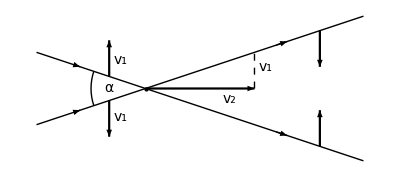

```mathematica
Block[{tachy,theta=ArcTan[1/3]},
tachy=Graphics[{
{PointSize[Large],Point[{{0,0}}]},
{Thickness[.0025],Line[{{-3,-1},{6,2}}]},
{Arrowheads[.02],Arrow[{.65{-3,-1},.6{-3,-1}}]},
{Arrowheads[.02],Arrow[{.6{6,2},.65{6,2}}]},
{Thickness[.0025],Line[{{-3,1},{6,-2}}]},
{Arrowheads[.02],Arrow[{.65{-3,1},.6{-3,1}}]},
{Arrowheads[.02],Arrow[{.6{6,-2},.65{6,-2}}]},
{Dashed,Line[{{3,0},{3,1}}]},
(*{Arrowheads[.03],Thickness[.004],Arrow[{{0,0},{0,1}}]},*)
{Arrowheads[.03],Thickness[.004],Arrow[{4{6,2}/5,4{6,2}/5+{0,-1}}]},
{Arrowheads[.035],Thickness[.004],Arrow[{{0,0},{3,0}}]},
{Arrowheads[.03],Thickness[.004],Arrow[{4{6,-2}/5,4{6,-2}/5+{0,1}}]},
{Arrowheads[.03],Thickness[.004],Arrow[{{-3,1}/3,{-3,1}/3+{0,1}}]},
{Arrowheads[.03],Thickness[.004],Arrow[{{-3,-1}/3,{-3,-1}/3+{0,-1}}]},
{Circle[{0,0},1.5,{-theta+π,theta+π}]},
Text[Style["α",14],{-1,0}],
Text[Style["v_2",14],{2.3,-.3}],
Text[Style["v_1",14],{-.7,.8}],
Text[Style["v_1",14],{-.7,-.8}],
Text[Style["v_1",14],{3.3,.6}]
}];
Export["/home/julian/mathematica/tachyonic-movement/TachMov.eps",tachy];
Export["/home/julian/latex/CVL-electron/Fig-1.eps",tachy];
tachy
]
```